Approx likelhood of going bust:

9.05 %

Mean and Median of outcomes:

51.8309

40

Chances of ending up ahead:

36.06 %

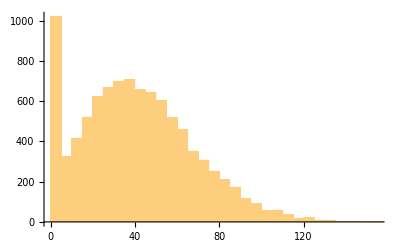

```mathematica
(*Initial Setup Here -
   hands and probabilities are in lists
	probabilities get accumlated up
	We then draw a random integer between 1-1000000
	as we have 6 signifigant digits here
	Each hand, we run a while loop checking if the
	random integer is less than the accumlated probabilty
	incrementing i each loop
	We will eventually hit this condition, at which point
	the value of i is set for us. We use i as the index
	to use when getting the result and payout.
 *)
hands = {"Natural Royal Flush","Four Deuces","Wild Royal Flush","Five of a kind", "Straight Flush","Four of a Kind","Full House","Flush","Straight","Three of a kind","Nothing"};
probs = {22,204,1796,3202,4168, 64938,21229,16784,56070,284690,546897};
payouts = {800,200,25,15,9,5,3,2,2,1,0};
weights = Accumulate[probs];

numSims = 10000;
walkAway =Table[
cash = 50;
turn = 0;
 i =1;
While[cash >0 && turn  < 200,
	cash--;
	hand = RandomInteger[1000000];
     i = 1;
    While[hand>weights[[i]],i++];
    cash += payouts[[i]];
    turn++
];
cash
,numSims
];

Busts = CountsBy[walkAway,LessEqualThan[0]][True];

Print["Approx likelhood of going bust: "]
N[Busts/numSims]*100 "%"
Print["Mean and Median of outcomes: "]
N[Mean[walkAway]]
Median[walkAway]
Print["Chances of ending up ahead: "]
N[CountsBy[walkAway,GreaterThan[50]][True]]/numSims*100 "%"
Histogram[walkAway]
```

```mathematica
T = 10;

ProfitFunc[n_,t_] := N[(750+(50*t))/(n+1)];
buildSims = 100000;

profits =Table[
curHotels = 0;
building = False;
profits = 0;
buildProfile = Table[
(* see if we can build *)
If[building, 
curHotels++;
building = False;
,
chance = RandomInteger[100];
If[chance≥ 50,
building = True;
,
building = False;
];
];
curHotels
,T
];
MapIndexed[ProfitFunc,buildProfile]
,buildSims];
simProfs = Map[Total,profits];
Mean[simProfs]
```

{4726.79}

```mathematica
rows = 10;
cols = 10;
board = RandomInteger[{0,1},{rows,cols}]
generations = 10

nextBoard = board;

Table[
board[[i,j]]
, {i,-1,1},j{1,-1}]
```

{{1,0,0,0,0,0,1,1,0,1},{1,0,1,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0,1,1},{1,1,0,1,0,0,0,1,0,0},{1,0,0,0,1,1,0,0,0,1},{0,0,1,0,1,1,1,1,0,1},{0,1,1,0,0,0,0,1,1,0},{0,0,0,1,1,0,0,0,0,0},{1,1,0,0,1,0,0,0,1,1},{0,1,0,0,1,0,0,1,1,0}}

10

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.